```mathematica
$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&;
Import[NotebookDirectory[]<>"../DiffGeoLib.m"]
```

Q1.

```mathematica
gPol = {{1,0},{0,r^2}};
gCart = {{1,0},{0,1}};
VPol = {A Cos[θ], B  Sin[θ]/r};
VPolDown = Table[Sum[gPol[[i,j]]VPol[[j]],{j,1,2}],{i,1,2}]
ExampleConsts = {A-> 1,B-> 1};
polCo = {r,θ};
cartCo = {x,y};
polInCart = {r-> Sqrt[x^2+y^2],r Cos[θ]-> x,r Sin[θ]-> y,θ-> ArcTan[x,y]};
cartInPol = {x-> r Cos[θ],y-> r Sin[θ]};
```

{A Cos[θ],B r Sin[θ]}

{(A x^2-B y^2)/(x^2+y^2),((A+B) x y)/(x^2+y^2)}

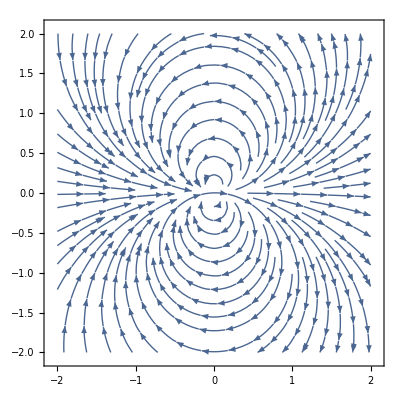

```mathematica
(*a*) 
VCart = FullSimplify[ConvertVector[VPolDown,polCo/.polInCart,cartCo]/.polInCart]
StreamPlot[VCart/.ExampleConsts,{x,-2,2},{y,-2,2}]
```

```mathematica
(*b*)
```

```mathematica
CovDPol = Table[CovariantD[VPol,{aa},{},gPol,polCo],{aa,{1,2}}]
```

(0 | -A Sin[θ]-B Sin[θ]
0 | (A Cos[θ])/r+(B Cos[θ])/r)

```mathematica
CovDCart = FullSimplify[Table[CovariantD[VCart,{},{aa},gCart,cartCo],{aa,{1,2}}]]
```

((2 (A+B) x y^2)/((x^2+y^2)^2) | -(2 (A+B) x^2 y)/((x^2+y^2)^2)
((A+B) y (-x^2+y^2))/((x^2+y^2)^2) | ((A+B) x (x-y) (x+y))/((x^2+y^2)^2))

((A+B) x)/(x^2+y^2)

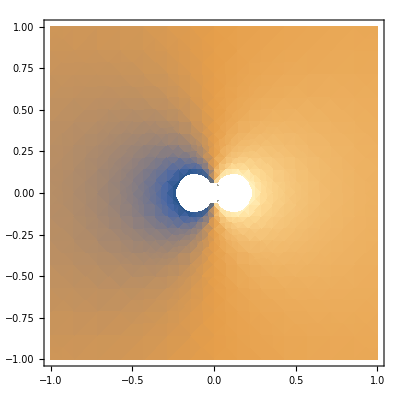

```mathematica
(*Plot the trace (divergence)*)
FullSimplify[Sum[CovDCart[[ii,ii]],{ii,1,2}]]
DensityPlot[%/.ExampleConsts,{x,-1,1},{y,-1,1}]
```

```mathematica
(*This checks if the two covariant derivatives are the same when converted to the same coordinate system*)

CovDPolDown = Table[Sum[CovDPol[[j,i]]gPol[[k,j]],{j,1,2}],{k,1,2},{i,1,2}]

CovDCart ==FullSimplify[Convert2Tensor[CovDPolDown,polCo/.polInCart,cartCo]/.polInCart]
```

(0 | -A Sin[θ]-B Sin[θ]
0 | r^2 ((A Cos[θ])/r+(B Cos[θ])/r))

True

```mathematica
(*c*)
```

The covariant derivative is zero if B=-A. Because the zero tensor is the same in all basis, the same A and B values give zero in both polar and Cartesian basis.

#### Problem 4

```mathematica
ClearAll["Global`*"]
```

```mathematica
g = A^2{{1,0},{0,Sin[θ]^2}};
coords = {θ,ϕ};
```

```mathematica
(*a*)
Γ[g,coords]
```

{{{0,0},{0,-Cos[θ] Sin[θ]}},{{0,Cot[θ]},{Cot[θ],0}}}

```mathematica
(*b*)
(*my code calcuates Subscript[R, abc]^d, so I contract weith the metric to lower the d.*)
FullSimplify[Table[Sum[g[[i,j]]RiemannTensor[g,coords][[a,b,c,j]],{j,1,2}],{i,1,2},{a,1,2},{b,1,2},{c,1,2}]]
```

{{{{0,0},{0,-A^2 Sin[θ]^2}},{{0,A^2 Sin[θ]^2},{0,0}}},{{{0,0},{A^2 Sin[θ]^2,0}},{{-A^2 Sin[θ]^2,0},{0,0}}}}

```mathematica
(*c*)
FullSimplify[RicciTensor[g,coords]]
FullSimplify[R[g,coords]]
```

(1 | 0
0 | Sin[θ]^2)

2/A^2

```mathematica
(*d*)
```

The Weyl tensor is zero, because the Riemann tensor contains all the information about the curvature.

```mathematica
FullSimplify[RiemannTensor[g,coords]]
FullSimplify[RiemannTensor[g,coords]][[2,1,2,1]]
```

{{{{0,0},{0,0}},{{0,1},{-Sin[θ]^2,0}}},{{{0,-1},{Sin[θ]^2,0}},{{0,0},{0,0}}}}

Sin[θ]^2

```mathematica
T = {0,1};
Table[Sum[RiemannTensor[g,coords][[aa,bb,cc,dd]]T[[aa]]x[[bb]]T[[cc]],{aa,1,2},{bb,1,2},{cc,1,2}],{dd,1,2}]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification x⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{x⟦1⟧ Sin[θ]^2,0}